Photon Counting Histograms (PCH) |

FPCHpaclet:Fretica/tutorial/PhotonCountingHistogramsPCH#40809785 | PCH fitting with Gratton-Zare model function (FPCH3DG)paclet:Fretica/tutorial/PhotonCountingHistogramsPCH#439763828
PCH fitting with FIDA model function (FPCHFida, FPCHFidaFit, FPCHFidaGlobalFit)paclet:Fretica/tutorial/PhotonCountingHistogramsPCH#40900141 |

```mathematica
Needs["Fretica`"]
```

```mathematica
FOpenTTTR[$FreticaExamples<>"\\Sim01.ht3"]
```

1

The data in "Sim01.ht3" were simulated assuming a  species concentration of c=50 pM  diffusing ( D=0.05 mm^2/ms.) through a laser focus described by a spherical-symmetric 3D Gaussian [   exp(-2r^2/w0^2) ] with w0=0.4 μm. The molecular brightness at the center of the confocal volume is 100 photons/ms.

The mean number of particles in the confocal volume calculates to π^(3/2)w0^3 c=0.0107
The  background is 1.5 photons/ms in the  acceptor channel and 3 photons/ms in the donor channel.

FPCH

```mathematica
?FPCH
```

```mathematica
FPCH[1(*ms*)]
```

-Graphics-

```mathematica
FPCH[1(*ms*),FOutput->FData]
```

{{0.,12838.},{1.,57707.},{2.,129779.},{3.,195155.},{4.,221247.},{5.,200774.},{6.,152243.},{7.,99507.},{8.,57333.},{9.,30073.},{10.,14848.},{11.,7395.},{12.,3741.},{13.,2168.},{14.,1472.},{15.,1199.},{16.,1039.},{17.,926.},{18.,763.},{19.,736.},{20.,645.},{21.,652.},{22.,560.},{23.,493.},{24.,460.},{25.,418.},{26.,433.},{27.,364.},{28.,367.},{29.,302.},{30.,298.},{31.,296.},{32.,256.},{33.,233.},{34.,257.},{35.,212.},{36.,220.},{37.,218.},{38.,163.},{39.,179.},{40.,157.},{41.,151.},{42.,149.},{43.,136.},{44.,126.},{45.,110.},{46.,120.},{47.,96.},{48.,93.},{49.,73.},{50.,69.},{51.,60.},{52.,54.},{53.,55.},{54.,55.},{55.,46.},{56.,37.},{57.,35.},{58.,39.},{59.,37.},{60.,33.},{61.,30.},{62.,22.},{63.,20.},{64.,27.},{65.,18.},{66.,17.},{67.,23.},{68.,18.},{69.,9.},{70.,9.},{71.,14.},{72.,10.},{73.,10.},{74.,7.},{75.,8.},{76.,5.},{77.,6.},{78.,4.},{79.,2.},{80.,7.},{81.,4.},{82.,3.},{83.,1.},{84.,1.},{85.,3.},{86.,2.},{87.,3.},{88.,3.},{89.,0.},{90.,1.},{91.,3.},{92.,2.},{93.,0.},{94.,2.},{95.,2.},{96.,0.},{97.,1.},{98.,0.},{99.,0.},{100.,0.},{101.,1.},{102.,0.},{103.,0.},{104.,0.},{105.,0.},{106.,0.},{107.,1.},{108.,0.},{109.,0.},{110.,0.},{111.,0.},{112.,0.},{113.,1.}}

```mathematica
FPCH[{1,0,0,0},1(*ms*)]
```

-Graphics-

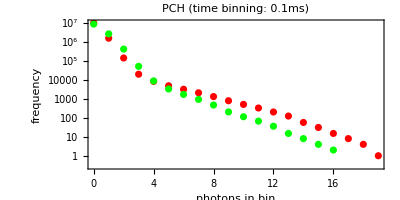

```mathematica
FPCH[{{1,0,0,0},{0,1,0,0}},0.1(*ms*),PlotStyle->{Red,Green}]
```

### PCH of the time interval {0, 100}

```mathematica
FPCH[{{1,0,0,0},{0,1,0,0}},0.1(*ms*),FTimeWindow->{0,100}]
```

-Graphics-

### PCH with lifetime channel constraints {3000,4096}

```mathematica
FLifeTimeHisto[FRoutes->{1,2},FPhotonData->All]
```

-Graphics-

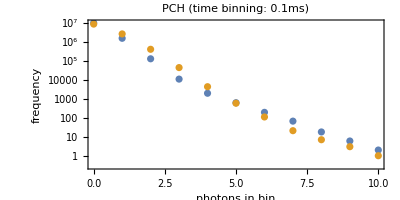

```mathematica
FPCH[{{1,0,0,0},{0,1,0,0}},0.1(*ms*),FChannelConstraints->{1,200}]
```

PCH fitting with FIDA model function (FPCHFida, FPCHFidaFit, FPCHFidaGlobalFit)

```mathematica
?FPCHFida
```

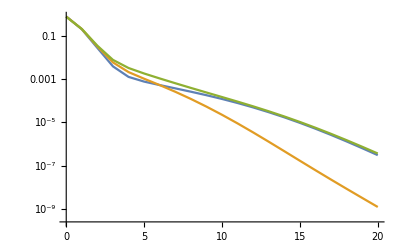

```mathematica
T=0.05(* binning in ms << mean diffusion time*);
ϵ1=200 (* molecular brightness at center of laser focus in 1/ms*);
ϵ2=100 ;
np1=0.01  (*mean particle number in confocal volume*);
np2=0.03  (*mean particle number in confocal volume*);
bg=5  (* background rate in 1/ms *);
nmax=20;
species1=FPCHFida[nmax,{{ ϵ1 T,np1}},bg T,{{1,0.5}(*3D Gaussian*)}];
species2=FPCHFida[nmax,{{ ϵ2 T,np2}},bg T,{{1,0.5}(*3D Gaussian*)}];
mixture=FPCHFida[nmax,{{ ϵ1 T,np1},{ ϵ2 T,np2}},bg T,{{1,0.5}(*3D Gaussian*)}];

ListLogPlot[{species1,species2,mixture},PlotRange->All,Joined->True]
```

```mathematica
?FPCHFidaFit
```

```mathematica
T=0.05(* binning in ms << mean diffusion time*);
pchdat=FPCH[T(*ms*),FOutput->FData];

(* initial guess values*)
ϵ=120;(* molecular brightness at center of laser focus in 1/ms*);
nparticle=0.1; (*mean particle number in confocal volume*);
bg=1; (* background rate in 1/ms *);

guess={{eps,ϵ},{np,nparticle},{nbg,bg},{a1,0.1},{a2,0.1}};

fitresult=FPCHFidaFit[pchdat,{{eps T,np}},nbg T,{{1,0.5}(*3D Gaussian*),{a1,1},{a2,2}},guess]
fitresult[[-1]]
```

-Graphics-

-Graphics-

```mathematica
?FPCHFidaGlobalFit
```

PCH fitting with Gratton-Zare model function (FPCH3DG)

```mathematica
?FPCH3DG
```

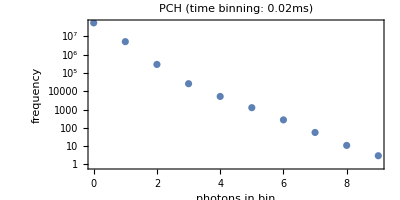

6.×10^7

```mathematica
T=0.02(* binning in ms << mean diffusion time*);
pl=FPCH[T]
pchdat=FPCH[T(*ms*),FOutput->FData];
nbins=Total[pchdat[[All,2]]] (* total number of bins *)
```

6.×10^7

{0.0005087,Null}

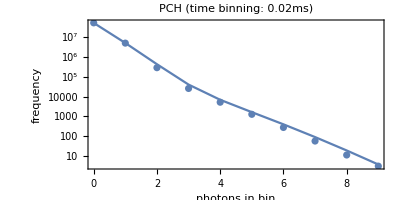

```mathematica
T=0.02(* binning in ms << mean diffusion time*);
pl=FPCH[T];
pchdat=FPCH[T(*ms*),FOutput->FData];
nbins=Total[pchdat[[All,2]]] (* total number of bins *)


ϵ=100;(* molecular brightness at center of laser focus in 1/ms*)
nmax=Length[pchdat]-1; (* pch is calculated up to nmax photons per bin *)
nparticle=0.02; (*mean particle number in confocal volume*)
bg=4.5; (* background rate in 1/ms *)
F1=1;F2=1; (* correction factors for deviation from 3D Gaussian focus *) ;

modelpch=FPCH3DG[nmax,{{ ϵ T,nparticle}},bg T,F1,F2];//AbsoluteTiming
modelpch[[All,2]]*=nbins;
Show[pl,ListLogPlot[{modelpch},PlotRange->All,Joined->True],PlotRange->All]
```

```mathematica
chisq[eps_?NumberQ,np_?NumberQ,nbg_?NumberQ]:=Module[{pch,σsqr},
pch=FPCH3DG[nmax,{{ eps T,np}},nbg T,F1,F2][[All,2]];
σsqr=nbins pch (1-pch);
Total[(nbins pch-pchdat[[All,2]])^2/σsqr]/(nmax-3)
] 
residuals[eps_?NumberQ,np_?NumberQ,nbg_?NumberQ]:=Module[{pch,σsqr},
pch=FPCH3DG[nmax,{{ eps T,np}},nbg T,F1,F2][[All,2]];
σsqr=nbins pch (1-pch);
(nbins pch-pchdat[[All,2]])/(√σsqr)
]
(*Yan Chen et al., Biophysical Journal Volume 77 July 1999 553–567  Eq.27*)
```

```mathematica
chisq[ϵ,nparticle,bg]
```

11153.6

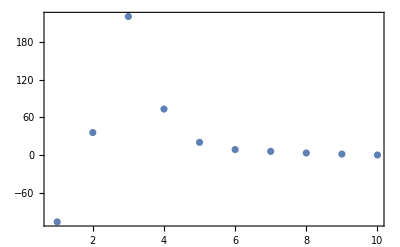

```mathematica
ListPlot[residuals[ϵ,nparticle,bg],Frame->True,PlotRange->All]
```

{750.099,{eps→147.66,np→0.00417657,nbg→4.64214}}

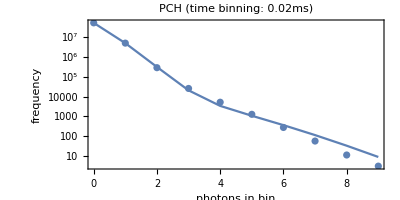

```mathematica
fitresult=FindMinimum[chisq[Abs@eps,Abs@np,Abs@nbg],{{eps,ϵ},{np,nparticle},{nbg,bg}},Method->"PrincipalAxis"]

modelpch=FPCH3DG[nmax,{{ Abs@eps T,Abs@np}},Abs@nbg T,F1,F2]/.fitresult[[2]];
modelpch[[All,2]]*=nbins;
Show[pl,ListLogPlot[{modelpch},PlotRange->All,Joined->True],PlotRange->All]
```

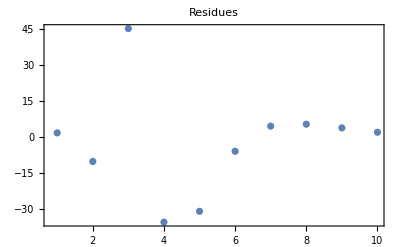

```mathematica
ListPlot[residuals[Abs@eps,Abs@np,Abs@nbg]/.fitresult[[2]],Frame->True,PlotRange->All,PlotLabel->"Residues"]
```

| Related Guides
▪Fretica